```mathematica
(*set path to the folder where input data for economy data, i.e. PWT data is located*). 
SetDirectory["C:...\\Economy_Population_Data"];
```

```mathematica
capdat=Import["capital_MER_data_PWT_Transposed.csv"];
capraw=capdat[[2;;]];
```

```mathematica
capraw2=capraw;
Do[Do[capraw2[[i,j]]=If[capraw[[i,j]]=="",0,capraw[[i,j]]],{i,2,71}],{j,2,181}]
lcapraw=Table[0,{i,71},{j,181}];
lcapraw[[1,1]]="year";
lcapraw[[1,2;;]]=capraw[[1,2;;]];
lcapraw[[2;;,1]]=capraw[[2;;,1]];
ncapraw=Table["",{i,181}];
rcap=Table[0,{i,181},{j,3}];
Do[ncapraw[[i]]=Position[capraw[[2;;,i]],_?(#≠""&),1,1][[1,1]]+1,{i,2,181}]
ncapraw[[141]]=52; (*for Russia we use the period from 2000 onwards to fit the data);*)
Do[lcapraw[[ncapraw[[i]];;,i]]=Log[capraw[[ncapraw[[i]];;,i]]]//N,{i,2,181}]
Do[rcap[[i,2]]=(lcapraw[[ncapraw[[i]]+15,i]]-lcapraw[[ncapraw[[i]],i]])/15,{i,2,181}]
Do[rcap[[i,3]]=(lcapraw[[71,i]]-lcapraw[[ncapraw[[i]],i]])/(71-ncapraw[[i]]),{i,2,181}]
rcap[[170,2]]=(lcapraw[[44,170]]-lcapraw[[42,170]])/2;
rcap[[170,3]]=(lcapraw[[44,170]]-lcapraw[[42,170]])/2;
rcap[[141,2]]=(lcapraw[[71,141]]-lcapraw[[57,141]])/(71-57);
rcap[[141,3]]=(lcapraw[[71,141]]-lcapraw[[57,141]])/(71-57);
Do[If[ncapraw[[i]]>2,{Do[lcapraw[[j,i]]=lcapraw[[ncapraw[[i]],i]]-rcap[[i,2]]*(ncapraw[[i]]-j),{j,2,ncapraw[[i]]-1}]},0],{i,2,181}]
```

```mathematica
(*Dimensions[Flatten[Position[ncapraw,2]]]*) (*number of countries with data from 1950 onward*)
(*Dimensions[Flatten[Position[ncapraw,_?(#<20&)]]]*)(*Number of countries with data starting <1968 onward availabe*)
```

```mathematica
capfull=Table[0,{i,71},{j,181}];
capfull[[1,1]]="year";
capfull[[1,2;;]]=capraw[[1,2;;]];
capfull[[2;;,1]]=capraw[[2;;,1]];
capfull[[2;;,2;;]]=Exp[lcapraw[[2;;,2;;]]];
```

```mathematica
Export["capital_MER_calc_full.csv",capfull]
```

capital_MER_calc_full.csv

```mathematica
captotal=Table[0,{i,71},{j,2}];
captotal[[1]]={"year","cap"};
Do[captotal[[i,1]]=1948+i,{i,2,71}]
Do[captotal[[i,2]]=Total[capfull[[i,2;;]]],{i,2,71}]
```

```mathematica
nexcap=Position[ncapraw,n_/;n>2];
noexcap=Position[ncapraw,n_/;n==2];
capnoextotal=Table[0,{i,71},{j,4}];
capnoextotal[[1]]={"year","cap","cap","cap"};
Do[capnoextotal[[i,1]]=1948+i,{i,2,71}]
Do[capnoextotal[[i,2]]=Total[capfull[[i,Flatten[noexcap]]]],{i,2,71}]
Do[capnoextotal[[i,3]]=Total[capfull[[i,Flatten[nexcap]]]],{i,2,71}]
Do[capnoextotal[[i,4]]=Total[capraw2[[i,Flatten[nexcap]]]],{i,2,71}]
```

```mathematica
fig1cap=ListLinePlot[{Legended[captotal[[2;;]],Placed["all countries",Below]],Legended[capnoextotal[[2;;,{1,2}]],Placed["wo extrapolated countries",Below]]},PlotStyle->{Blue,Black},PlotLabel->"Capital Stock MER",ImageSize->600];
(*Export["fig1_cap.pdf",fig1cap]*)
```

```mathematica
captotal[[71]]
```

{2019,5.62113×10^8}

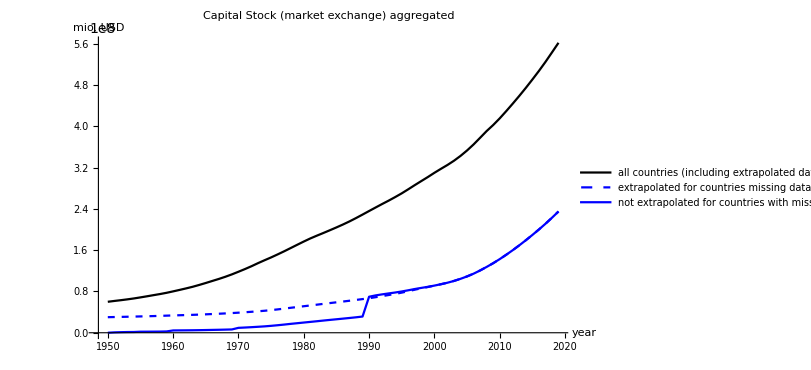

```mathematica
fig2cap=ListLinePlot[{Legended[captotal[[2;;]],Placed["all countries (including extrapolated data)",Below]],Legended[capnoextotal[[2;;,{1,3}]],Placed["extrapolated for countries missing data",Below]],Legended[capnoextotal[[2;;,{1,4}]],Placed["not extrapolated for countries with missing data",Below]]},PlotStyle->{Black,{Blue,Dashed},Blue},AxesLabel->{"year","mio. USD"},PlotLabel->"Capital Stock (market exchange) aggregated",ImageSize->600]
```

```mathematica
Export["fig2_cap.eps",fig2cap]
```

fig2_cap.eps

```mathematica
caprates=Table[0,{i,71},{j,181}];
caprates[[1,1]]="year";
caprates[[1,2;;]]=capraw[[1,2;;]];
caprates[[2;;,1]]=capraw[[2;;,1]];
Do[caprates[[i,2;;]]=capfull[[i,2;;]]/capfull[[71,2;;]],{i,2,71}]
```

## Output Data at Market Exchange Rates

```mathematica
outdat=Import["output_MER_data_PWT_Transposed.csv"];
Dimensions[outdat]
outraw=outdat[[2;;,;;]];
Dimensions[outraw]
```

{72,181}

{71,181}

```mathematica
loutraw=Table[0,{i,71},{j,181}];
loutraw[[1,1]]="year";
loutraw[[1,2;;]]=outraw[[1,2;;]];
loutraw[[2;;,1]]=outraw[[2;;,1]];
noutraw=Table["",{i,181}];
Do[noutraw[[i]]=Position[outraw[[2;;,i]],_?(#≠""&),1,1][[1,1]]+1,{i,2,181}]
(*noutraw[[141]]=52; (*for Russia we use the period from 2000 onwards to fit the data);*)*)
rout=Table[0,{i,181},{j,3}];
Do[loutraw[[noutraw[[i]];;,i]]=Log[outraw[[noutraw[[i]];;,i]]]//N,{i,2,181}]
Do[rout[[i,2]]=(loutraw[[noutraw[[i]]+15,i]]-loutraw[[noutraw[[i]],i]])/15,{i,2,181}]
Do[rout[[i,3]]=(loutraw[[71,i]]-loutraw[[noutraw[[i]],i]])/(71-noutraw[[i]]),{i,2,181}]
rout[[170,2]]=(loutraw[[65,170]]-loutraw[[50,170]])/2;
rout[[170,3]]=(loutraw[[71,170]]-loutraw[[50,170]])/2;
rout[[141,2]]=(loutraw[[71,141]]-loutraw[[57,141]])/(71-57);
rout[[141,3]]=(loutraw[[71,141]]-loutraw[[57,141]])/(71-57);
Do[If[noutraw[[i]]>2,{Do[loutraw[[j,i]]=loutraw[[noutraw[[i]],i]]-rout[[i,3]]*(noutraw[[i]]-j),{j,2,noutraw[[i]]-1}]},0],{i,2,181}]
```

```mathematica
Export["outfull_MER_calc_full.csv",outfull]
```

outfull_MER_calc_full.csv

```mathematica
outraw2=outraw;
Do[Do[outraw2[[i,j]]=If[outraw[[i,j]]=="",0,outraw[[i,j]]],{i,2,71}],{j,2,181}]
```

```mathematica
outfull=Table[0,{i,71},{j,181}];
outfull[[1,1]]="year";
outfull[[1,2;;]]=outraw[[1,2;;]];
outfull[[2;;,1]]=outraw[[2;;,1]];
outfull[[2;;,2;;]]=Exp[loutraw[[2;;,2;;]]];
outtotal=Table[0,{i,71},{j,2}];
outtotal[[1]]={"year","cap"};
Do[outtotal[[i,1]]=1948+i,{i,2,71}]
Do[outtotal[[i,2]]=Total[outfull[[i,2;;]]],{i,2,71}]
```

```mathematica
noexout=Position[noutraw,2];
nexout=Position[noutraw,n_/;n>2];
outnoextotal=Table[0,{i,71},{j,4}];
outnoextotal[[1]]={"year","cap","cap","cap"};
Do[outnoextotal[[i,1]]=1948+i,{i,2,71}]
Do[outnoextotal[[i,2]]=Total[outfull[[i,Flatten[noexout]]]],{i,2,71}]
Do[outnoextotal[[i,3]]=Total[outfull[[i,Flatten[nexout]]]],{i,2,71}]
Do[outnoextotal[[i,4]]=Total[outraw2[[i,Flatten[nexout]]]],{i,2,71}]
```

```mathematica
(*fig1out=ListLinePlot[{Legended[outtotal[[2;;]],Placed["all countries",Below]],Legended[outnoextotal[[2;;,{1,2}]],Placed["wo extrapolated countries",Below]]},PlotStyle->{Blue,Black},PlotLabel->"Output MER",ImageSize->600];
Export["fig3_out.pdf",fig1out]*)
```

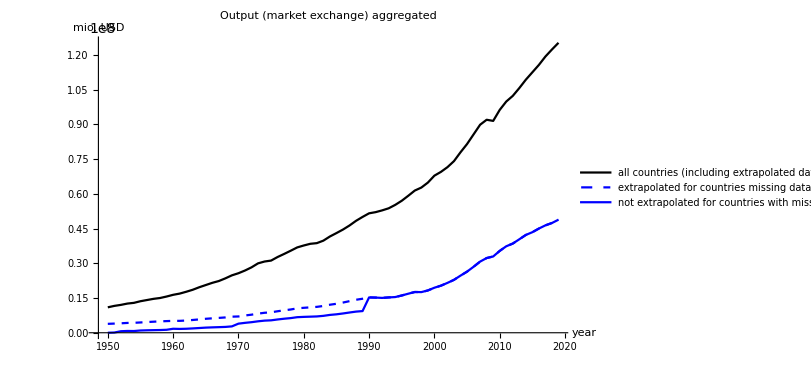

```mathematica
fig2out=ListLinePlot[{Legended[outtotal[[2;;]],Placed["all countries (including extrapolated data)",Below]],Legended[outnoextotal[[2;;,{1,3}]],Placed["extrapolated for countries missing data",Below]],Legended[outnoextotal[[2;;,{1,4}]],Placed["not extrapolated for countries with missing data",Below]]},PlotStyle->{Black,{Blue,Dashed},Blue},AxesLabel->{"year","mio. USD"},PlotLabel->"Output (market exchange) aggregated",ImageSize->600]
```

```mathematica
Export["fig4_out.eps",fig2out]
```

fig4_out.eps

```mathematica
outrate=Table[0,{i,71},{j,181}];
outrate[[1,1]]="year";
outrate[[1,2;;]]=outfull[[1,2;;]];
outrate[[2;;,1]]=outfull[[2;;,1]];
Do[outrate[[i,2;;]]=outfull[[i,2;;]]/outfull[[71,2;;]],{i,1,71}]
```

```mathematica
capPPPraw=Import["capital_PPP_data_PWT_Transposed.csv"];
Dimensions[capPPPraw]
outPPP2019raw=Import["output_PPP_data_PWT_only2019_Transposed.csv"];
Dimensions[outPPP2019raw]
```

{71,181}

{2,181}

```mathematica
capPPPcalc=Table[0,{i,71},{j,181}];
capPPPcalc[[1,1]]="year";
capPPPcalc[[2;;,1]]=capPPPraw[[2;;,1]];
capPPPcalc[[1,2;;]]=capPPPraw[[1,2;;]];
capPPP2019=capPPPraw[[71,2;;]];
Do[capPPPcalc[[i,2;;]]=capPPP2019*caprates[[i,2;;]],{i,2,71}]
```

```mathematica
capPPPtotal=Table[0,{i,71},{j,3}];
capPPPtotal[[1]]={"year","cap","diff"};
Do[capPPPtotal[[i,1]]=1948+i,{i,2,71}]
Do[capPPPtotal[[i,2]]=Total[capPPPcalc[[i,2;;]]],{i,2,71}]
capPPPtotal[[2;;,3]]=capPPPtotal[[2;;,2]]-captotal[[2;;,2]];
```

```mathematica
Export["capital_PPP_calc_full.csv",capPPPcalc]
```

capital_PPP_calc_full.csv

```mathematica
(*fig1PPPcap=ListLinePlot[{Legended[captotal[[2;;,{1,2}]],Placed["Marked Exchange",Below]],Legended[capPPPtotal[[2;;,{1,2}]],Placed["PPP",Below]]},PlotStyle->{Blue,Orange},PlotLabel->"Capital Stocks MER versus PPP",ImageSize->600],Export["fig5_capPPP.pdf",fig1PPPcap]*)
```

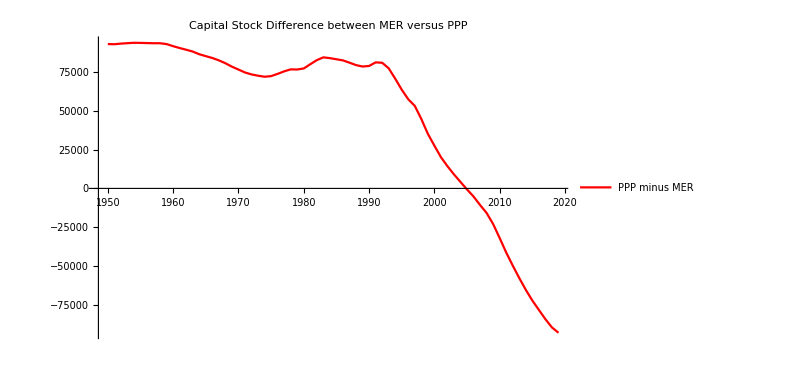

```mathematica
fig2PPPcap=ListLinePlot[{Legended[capPPPtotal[[2;;,{1,3}]],Placed["PPP minus MER",Below]]},PlotStyle->{Red},PlotLabel->"Capital Stock Difference between MER versus PPP",ImageSize->600]
```

```mathematica
Export["fig6_capPPP.pdf",fig2PPPcap]
```

fig6_capPPP.pdf

```mathematica
outPPPcalc=Table[0,{i,71},{j,181}];
outPPPcalc[[1,1]]="year";
outPPPcalc[[2;;,1]]=capPPPraw[[2;;,1]];
outPPPcalc[[1,2;;]]=capPPPraw[[1,2;;]];
outPPP2019=outPPP2019raw[[2,2;;]];
Do[outPPPcalc[[i,2;;]]=outPPP2019*outrate[[i,2;;]],{i,2,71}]
```

```mathematica
Export["output_PPP_calc_full.csv",outPPPcalc]
```

output_PPP_calc_full.csv

```mathematica
outPPPtotal=Table[0,{i,71},{j,3}];
outPPPtotal[[1]]={"year","cap","diff"};
Do[outPPPtotal[[i,1]]=1948+i,{i,2,71}]
Do[outPPPtotal[[i,2]]=Total[outPPPcalc[[i,2;;]]],{i,2,71}]
outPPPtotal[[2;;,3]]=outPPPtotal[[2;;,2]]-outtotal[[2;;,2]];
```

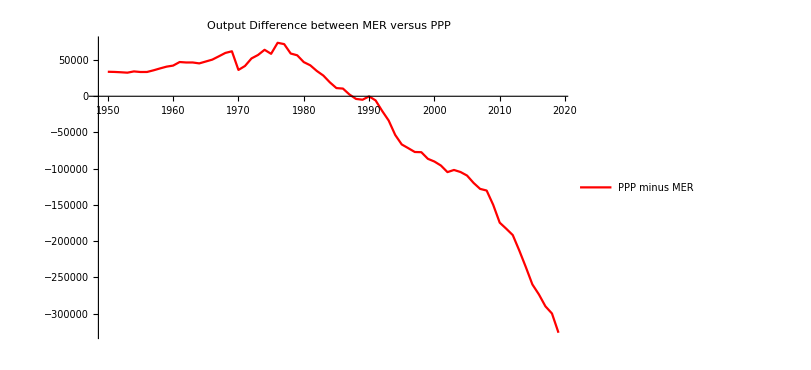

```mathematica
fig1PPPout=ListLinePlot[{Legended[outPPPtotal[[2;;,{1,3}]],Placed["PPP minus MER",Below]]},PlotStyle->{Red},PlotLabel->"Output Difference between MER versus PPP",ImageSize->600]
```

```mathematica
Export["fig7_outPPP.pdf",fig1PPPout]
```

fig7_outPPP.pdf

```mathematica
depdat=Import["depreciation_data_PWT_Transposed.csv"];
Dimensions[depdat]
depraw=depdat[[2;;,;;]];
Dimensions[depraw]
```

{72,181}

{71,181}

```mathematica
dnraw=Table["",{i,181},{j,2}];
Do[dnraw[[i,1]]=Position[depraw[[2;;,i]],_?(#≠""&),1,1][[1,1]]+1,{i,2,181}]
Do[dnraw[[i,2]]=depraw[[dnraw[[i,1]],i]],{i,2,181}]
depfull=depraw;
Do[Do[depfull[[i,j]]=dnraw[[j,2]],{i,2,dnraw[[j,1]]}],{j,2,181}]
(*use the last observed deprecition value for the missing data*)
```

```mathematica
depraw2=depraw;
Do[Do[depraw2[[i,j]]=If[depraw[[i,j]]=="",0,depraw[[i,j]]],{i,2,71}],{j,2,181}]
capPPPraw2=capPPPraw;
Do[Do[capPPPraw2[[i,j]]=If[capPPPraw[[i,j]]=="",0,capPPPraw[[i,j]]],{i,2,71}],{j,2,181}]
(*do not consider deprecition rates of missing countries*)
```

```mathematica
depweight=Table[0,{i,71},{j,3}];
depweight[[1]]={"year","totalCap","weightedD"};
Do[depweight[[i,1]]=1948+i,{i,2,71}]
Do[depweight[[i,2]]=Total[capPPPraw2[[i,2;;]]],{i,2,71}]
Do[depweight[[i,3]]=Total[capPPPraw2[[i,2;;]]*depraw2[[i,2;;]]]/depweight[[i,2]],{i,2,71}]
```

```mathematica
depweight2=Table[0,{i,71},{j,3}];
depweight2[[1]]={"year","totalCap","weightedD"};
Do[depweight2[[i,1]]=1948+i,{i,2,71}]
Do[depweight2[[i,2]]=Total[capPPPcalc[[i,2;;]]],{i,2,71}]
Do[depweight2[[i,3]]=Total[capPPPcalc[[i,2;;]]*depfull[[i,2;;]]]/depweight2[[i,2]],{i,2,71}]
```

```mathematica
(*fig1deprec=ListLinePlot[{Legended[depweight[[2;;,{1,3}]],Placed["weightd delta",Below]]},PlotStyle->{Red},PlotLabel->"observed PPP capital weighted depreciation rate",ImageSize->600]*)
```

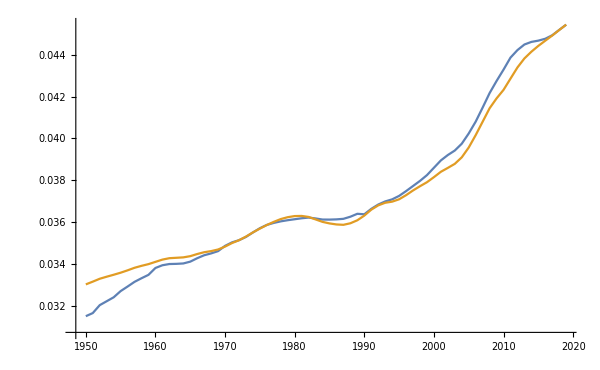

```mathematica
ListLinePlot[{depweight[[2;;,{1,3}]],depweight2[[2;;,{1,3}]]},ImageSize->600]
```

```mathematica
GeometricMean[depweight2[[2;;,3]]]
GeometricMean[depweight[[2;;,3]]]
```

0.0370621

0.0370395

```mathematica
results=Table[0,{i,71},{j,14}];
results[[1]]={"1_year","2_Cap_MER","3_Cap_PPP","4_Out_MER","5_out_PPP","6_deprec","7_I_MER_dcon","8_I_PPP_dcon","9_I_MER_dtime","10_C_PPP_dtime","11_C_MER_dcon","12_C_PPP_dcon","13_C_MER_dtime","14_C_PPP_dtime"};
Do[results[[i,1]]=1948+i,{i,2,71}]
results[[2;;,2]]=captotal[[2;;,2]]/10^6;
results[[2;;,3]]=capPPPtotal[[2;;,2]]/10^6;
results[[2;;,4]]=outtotal[[2;;,2]]/10^6;
results[[2;;,5]]=outPPPtotal[[2;;,2]]/10^6;
results[[2;;,6]]=depweight2[[2;;,3]];
Do[results[[i,7]]=results[[i+1,2]]-results[[i,2]]*(1-0.037),{i,2,70}]
Do[results[[i,8]]=results[[i+1,3]]-results[[i,3]]*(1-0.037),{i,2,70}]
Do[results[[i,9]]=results[[i+1,2]]-results[[i,2]]*(1-results[[i,6]]),{i,2,70}]
Do[results[[i,10]]=results[[i+1,3]]-results[[i,3]]*(1-results[[i,6]]),{i,2,70}]
results[[2;;,11]]=results[[2;;,4]]-results[[2;;,7]];
results[[2;;,12]]=results[[2;;,5]]-results[[2;;,8]];
results[[2;;,13]]=results[[2;;,4]]-results[[2;;,9]];
results[[2;;,14]]=results[[2;;,5]]-results[[2;;,10]];
```

```mathematica
Export["Results_PPP_calculated_Aggregated.csv",results]
```

Results_PPP_calculated_Aggregated.csv

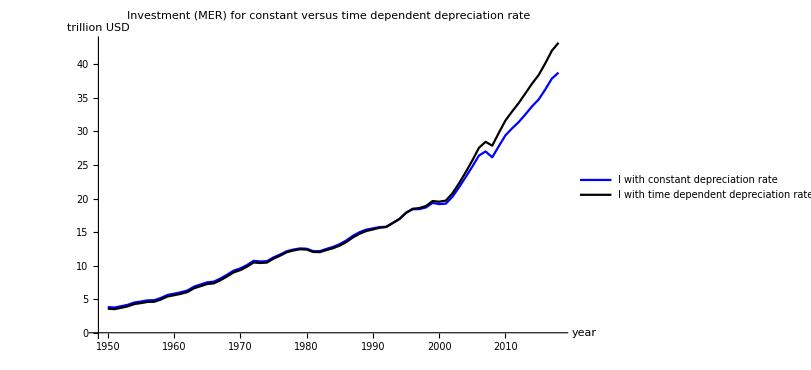

```mathematica
fig1results=ListLinePlot[{Legended[results[[2;;70,{1,7}]],Placed["I with constant depreciation rate",Below]],Legended[results[[2;;70,{1,9}]],Placed["I with time dependent depreciation rate",Below]]},PlotStyle->{Blue,Black},AxesLabel->{"year","trillion USD"},PlotLabel->"Investment (MER) for constant versus time dependent depreciation rate",ImageSize->600]
```

```mathematica
Export["fig9_comparison_investment.eps",fig1results]
```

fig9_comparison_investment.eps

```mathematica
(*lshareraw=Import["labor_share_PWT_Transposed.csv"];
Dimensions[lshareraw];
lshare=lshareraw[[2;;,;;]];
Dimensions[lshare];
Dimensions[outraw];
lnraw=Table["",{i,181},{j,3}];
Do[lnraw[[i,1]]=Position[lshare[[2;;,i]],_?(#≠""&),1,1][[1,1]]+1,{i,2,181}]
Do[lnraw[[i,2]]=lshare[[dnraw[[i,1]],i]],{i,2,181}]
lfull=lshare;
Do[Do[lfull[[i,j]]=lnraw[[j,2]],{i,2,lnraw[[j,1]]}],{j,2,181}]
lfull2=lshare;
Do[Do[lfull2[[i,j]]=If[lshare[[i,j]]=="",0,lshare[[i,j]]],{i,2,71}],{j,2,181}]
outPPPcalc2=outPPPcalc;
(*Do[Do[outPPPcalc2[[i,j]]=If[lshare[[i,j]]=="",0,outPPPcalc2[[i,j]]],{i,2,71}],{j,2,181}]*)
Do[lnraw[[i,2]]=lshare[[dnraw[[i,1]],i]],{i,2,181}]
lfull=lshare;
Do[Do[lfull[[i,j]]=lnraw[[j,2]],{i,2,lnraw[[j,1]]}],{j,2,181}]
lfull2=lshare;
Do[Do[lfull2[[i,j]]=If[lshare[[i,j]]=="",0,lshare[[i,j]]],{i,2,71}],{j,2,181}]
outPPPcalc2=outPPPcalc;
(*Do[Do[outPPPcalc2[[i,j]]=If[lshare[[i,j]]=="",0,outPPPcalc2[[i,j]]],{i,2,70}],{j,2,181}]*)
Do[Do[outPPPcalc2[[i,j]]=If[lfull2[[i,j]]==0,0,outPPPcalc2[[i,j]]],{i,2,71}],{j,2,181}]
(*Do[outPPPcalc2[[71,j]]=If[lshare[[71,j]]==0,0,outPPPcalc2[[71,j]]],{j,2,70}]*)
lsweight=Table[0,{i,71},{j,3}];
lsweight[[1]]={"year","totalOut","weightedLS"};
Do[lsweight[[i,1]]=1948+i,{i,2,71}]
Do[lsweight[[i,2]]=Total[outPPPcalc2[[i,2;;]]],{i,2,71}]
Do[lsweight[[i,3]]=Total[outPPPcalc2[[i,2;;]]*lfull2[[i,2;;]]]/lsweight[[i,2]],{i,2,71}]
kappa1=1-Mean[lsweight[[61;;71,3]]]
kappa2=1-Mean[lsweight[[71;;71,3]]]
kappa3=1-Mean[lsweight[[2;;,3]]]*)
```

```mathematica
returnraw=Import["realreturn_data_PWT_transposed.csv"];
Dimensions[returnraw]
return=returnraw[[2;;,;;]];
Dimensions[return]
Dimensions[capfull]
```

{72,181}

{71,181}

{71,181}

```mathematica
capfullreturn=capfull;
Do[Do[capfullreturn[[i,j]]=If[return[[i,j]]==0,0,capfull[[i,j]]],{i,2,71}],{j,2,181}]
outfullreturn=outfull;
Do[Do[outfullreturn[[i,j]]=If[return[[i,j]]==0,0,outfull[[i,j]]],{i,2,71}],{j,2,181}]
rweight=Table[0,{i,71},{j,6}];
rweight[[1]]={"year","totalcap","totalout","weightedLS","cap_out_ratio","alpha"};
Do[rweight[[i,1]]=1948+i,{i,2,71}]
Do[rweight[[i,2]]=Total[capfullreturn[[i,2;;]]],{i,2,71}]
Do[rweight[[i,3]]=Total[outfullreturn[[i,2;;]]],{i,2,71}]
Do[rweight[[i,4]]=Total[capfullreturn[[i,2;;]]*return[[i,2;;]]]/rweight[[i,2]],{i,2,71}](*capital weighted real return on capital*)
rweight[[2;;,5]]=rweight[[2;;,2]]/rweight[[2;;,3]];(*capital-output-ratio*)
rweight[[2;;,6]]=rweight[[2;;,4]]*rweight[[2;;,2]]/rweight[[2;;,3]];
```

```mathematica
GeometricMean[rweight[[2;;,6]]] (*capital fraction in Cobb-Douglas Production function*)
```

0.393133